```mathematica
M1=10;M2=5;Q=10;
```

```mathematica
s=Table[RandomInteger[{2,255}]/256.,{Q},{M1}];
```

```mathematica
S=Exp[I 2 Pi s];
```

```mathematica
r=Table[RandomInteger[{1,256}]/256.,{Q},{M2}];
```

```mathematica
R=Exp[I 2 Pi r];
```

```mathematica
X0=Table[Exp[I RandomInteger[{1,256}]/256.],{M1},{M2}];
```

```mathematica
(*Lernen auf der Testmenge:*)
```

```mathematica
X=X0;
```

```mathematica
Do[X=X+Outer[Times,Conjugate[S[[i]]],(R[[i]]-1/M1*S[[i]].X)],{i,1,Q}];
```

```mathematica
(*Zuordnung und Fehlerberechnung nach jeder Lernperiode:*)
```

```mathematica
STest=S[[1]];
```

```mathematica
rgoal=r[[1]];
```

```mathematica
X=X0;
```

```mathematica
TT=Table[Do[X=X+Outer[Times,Conjugate[S[[i]]],(R[[i]]-1/M1*S[[i]].X)],{i,1,Q}];
rneu=Mod[Arg[(1/M1 STest.X)]/(2 Pi),1];((rneu-rgoal).(rneu-rgoal))^0.5/M2,{10}]
```

{0.0522481,0.060476,0.0619632,0.0623156,0.0624172,0.062194,0.0616538,0.0608988,0.0600432,0.059175}

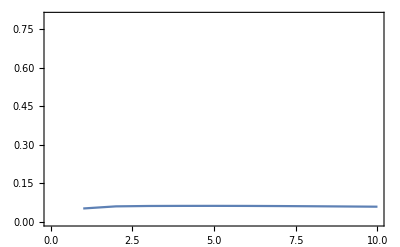

```mathematica
ListPlot[TT,Frame->True,Axes->None,Joined->True,PlotRange->{0,0.8}]
```

```mathematica
(*Für ganze Lernepochen von verrauschten Bildern sieht das wie folgt aus:*)
```

```mathematica
X=X0;
```

```mathematica
rr=0;
```

```mathematica
Do[
S[[i]]=Exp[I 2 Pi (s[[i]]+Table[fnoise[sigmal],{M1}])];
X=X+Outer[Times,Conjugate[S[[i]]],(R[[i]]-1/M1*S[[i]].X)],
{i,1,Q}];
```

$Aborted

```mathematica
Do[STest=S[[iii]];
TTT=Table[rneu=Mod[Arg[(1/M1 STest.X)]/(2 Pi),1]+Table[fnoise[sigmar],{M2}];((rneu-r[[jjj]]).(rneu-r[[jjj]]))^0.5/M2,{jjj,1,Q}];
mi=Min[TTT];
If[Flatten[Position[TTT,mi]]=={iii},rr++ 1,];,{iii,1,Q}];
rr=N[rr/Q],{Epochs}]
```

$Aborted